# Fit vertex angles in experiments, measure domain sizes, and the number of vertices (corners) of each domain

Change data directory

```mathematica
movie=Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/180427_ch1_2uM-MinD_8uM-E-His_timeseries01.lsm"][[1,All,1]];
```

Separate MinD and MinE channels

```mathematica
movieSep=(ColorSeparate[#])&/@movie;
```

Average two consecutive snapshots to reduce noise

```mathematica
movieAvg={ImageAdd[#[[1,1]],#[[2,1]]],ImageAdd[#[[1,2]],#[[2,2]]]}&/@Partition[movieSep,2,1];
```

## Image preparation

### MinD-MinE pixel clustering (image at initial time)

```mathematica
classImage=BrightnessEqualize[ImageAdjust[#]]&/@movieAvg[[1]];
```

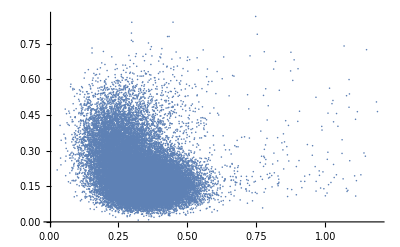

```mathematica
ListPlot[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}[[All,;;200,;;200]]],PlotRange->All]
```

```mathematica
clusters=FindClusters[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}],2,Method->"KMeans",DistanceFunction->EuclideanDistance];
```

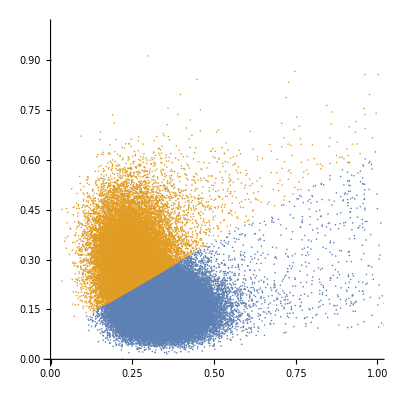

```mathematica
ListPlot[clusters[[All,;;;;10]],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

```mathematica
centroids=Mean/@clusters;
```

```mathematica
ratioDE=#[[1]]/#[[2]]&@First@Differences[centroids]
```

-0.572725

### Mesh binarization

```mathematica
ClearAll@meshBinarize;
Options[meshBinarize]={"ThresholdPixelNumber"->10};
meshBinarize[img_,ratioDE_,opts:OptionsPattern[]]:=Block[
{imgEq=BrightnessEqualize[ImageAdjust[#]]&/@img,
minDMeas,
minE,
minD,
imgProj,
imgBinarized,
morphImg,
smallComponents,
morphMask,
imgBinarizedCleaned
},
minDMeas=ImageMeasurements[imgEq[[2]],{"Mean","StandardDeviation"}];
minE=imgEq[[1]];
(*to ignore MinD aggregates, cut brightness at mean+std off*)
minD=ImageClip[imgEq[[2]],{0,Total@minDMeas}];
(*project pixel MinD MinE fluorescence values on the axis connecting the centroids of the clusters identified in the initial image*)
imgProj=Image[ImageData[minE]+ratioDE ImageData[minD]];
(*binarize along this axis, and smooth to get a connected mesh*)
imgBinarized=Binarize[GaussianFilter[Binarize[ImageAdjust@imgProj],5],0.3];

(*remove too small morphological components*)
morphImg=MorphologicalComponents[imgBinarized];
smallComponents=Keys@Select[ComponentMeasurements[morphImg,"Area"],#[[2]]<10&];
morphMask=Clip[morphImg/.Thread[smallComponents->-1],{-1,0}];
imgBinarizedCleaned=Image[ImageData[imgBinarized]+morphMask];

{imgProj,imgBinarizedCleaned}
]
```

#### Analyze movie

```mathematica
movieProj=meshBinarize[#,ratioDE]&/@movieAvg;
```

```mathematica
Export[NotebookDirectory[]<>"movieProj1.tiff",movieProj[[All,1]]];
```

```mathematica
Export[NotebookDirectory[]<>"movieProj2.tiff",movieProj[[All,2]]];
```

```mathematica
(*movieProj1=Import[NotebookDirectory[]<>"movieProj1.tiff"];*)
```

```mathematica
(*movieProj2=Import[NotebookDirectory[]<>"movieProj2.tiff"];*)
```

```mathematica
(*movieProj=Transpose[{movieProj1,movieProj2}];*)
```

```mathematica
movieProj[[1,1]]
```

```mathematica
movieProj[[1,2]]
```

## Vertex statistics

## Determine branch points

The branch width is about 5 pixels.
We prun branches shorter than 10 pixels because do not reliably describe separate branches (repeatedly to account for short, branched segments that we want to remove).

```mathematica
branchMov=Binarize[Thinning[Pruning[Pruning[Pruning[Thinning[#[[2]]],10],10],10]]]&/@movieProj;
```

```mathematica
Export[NotebookDirectory[]<>"branchMov.tiff",branchMov];
```

```mathematica
branchPoints=MorphologicalBranchPoints[#]&/@branchMov;
```

```mathematica
branchPointCoords=ImageValuePositions[#,1]&/@branchPoints;
```

```mathematica
HighlightImage[branchMov[[1]],{AbsolutePointSize[3],branchPointCoords[[1]]}]
```

## Domain statistics

Determine the domains alone:

```mathematica
domainMov=Pruning[#,Infinity]&/@branchMov;
```

```mathematica
domainMov[[1]]
```

```mathematica
Export[NotebookDirectory[]<>"domainMov.tiff",domainMov];
```

```mathematica
(*domainMov=Import[NotebookDirectory[]<>"domainMov.tiff"];*)
```

```mathematica
domains=MorphologicalComponents[ColorNegate@ImagePad[#,1],"CornerNeighbors"->False]&/@domainMov;
```

```mathematica
domains[[1]]//Colorize
```

## Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481
```

0.212548

```mathematica
domainMeas=SortBy[ComponentMeasurements[#,{"Centroid","Area","Holes"}],Values[#][[2]]&][[;;-2]]&/@domains;
```

```mathematica
Manipulate[Histogram[{dx^2Select[Values[domainMeas[[Floor@i]]][[domainInds[[Floor@i,All,1]],2;;]],#[[2]]==0&][[All,1]],dx^2Select[Values[domainMeas[[Floor@i]]][[domainInds[[Floor@i,All,1]],2;;]],#[[2]]>=1&][[All,1]]},{0,250,10}],{i,1,99}]
```

## Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
cornerNumber=ParallelTable[
Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains[[t]],{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints[[t]],mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,Keys[domainMeas[[t]]]}],
{t,Length@domains},Method->"FinestGrained"];
```

```mathematica
Manipulate[Histogram[cornerNumber[[Floor@i]],{0.5,10,1}],{i,1,99}]
```

```mathematica
N/@Mean/@cornerNumber
```

{5.8119,5.8128,5.80235,5.79433,5.77672,5.80189,5.78873,5.77594,5.75352,5.79206,5.75463,5.74419,5.74592,5.7321,5.70046,5.71724,5.70413,5.69406,5.72414,5.71264,5.68578,5.69565,5.72414,5.70252,5.72311,5.71396,5.71461,5.72273,5.71946,5.70522,5.73864,5.72789,5.73469,5.73649,5.71106,5.70562,5.69977,5.72235,5.72523,5.72072,5.72624,5.7236,5.72748,5.73318,5.7236,5.73649,5.70022,5.70246,5.68597,5.72383,5.71205,5.67849,5.72098,5.70824,5.68973,5.71018,5.70354,5.72062,5.72185,5.68653,5.68363,5.70133,5.72467,5.68202,5.70989,5.7011,5.68271,5.6841,5.69935,5.70652,5.68478,5.70217,5.68547,5.64565,5.68251,5.69114,5.65739,5.68387,5.64592,5.66026,5.67452,5.66595,5.65598,5.66951,5.64544,5.66311,5.65957,5.65885,5.68657,5.67094,5.67094,5.65745,5.65605,5.68008,5.67511,5.66596,5.70339,5.67516,5.6723}

```mathematica
N/@StandardDeviation/@cornerNumber
```

{1.26089,1.30066,1.26398,1.32878,1.29744,1.25229,1.27877,1.29713,1.24911,1.23426,1.22047,1.23456,1.22789,1.18724,1.19763,1.19544,1.18499,1.194,1.16881,1.17489,1.16654,1.14991,1.16288,1.16064,1.1726,1.16253,1.15535,1.15946,1.17534,1.15962,1.18355,1.14945,1.15597,1.16976,1.16415,1.1802,1.15052,1.15423,1.16037,1.16318,1.14867,1.13006,1.16768,1.14485,1.14786,1.14636,1.15194,1.15544,1.13657,1.09152,1.09489,1.11194,1.09312,1.12081,1.10305,1.11931,1.09653,1.10433,1.13371,1.10258,1.10206,1.09896,1.11044,1.09634,1.10037,1.07776,1.08921,1.07897,1.10033,1.10394,1.08193,1.11652,1.09086,1.07176,1.08545,1.07996,1.08163,1.07331,1.0802,1.10767,1.09479,1.09808,1.08682,1.11111,1.1164,1.1159,1.11926,1.10691,1.09479,1.0983,1.09047,1.09841,1.084,1.12366,1.12624,1.10202,1.10632,1.09282,1.10297}

#### cornerNumberList

```mathematica
cornerNumber
```

## Analyze domain-area trajectories

```mathematica
domainVals=(Join[#[[1]],{#[[2]]}]&/@Transpose[{Values[#[[1]]],#[[2]]}])&/@Transpose[{domainMeas,cornerNumber}];
```

```mathematica
times=10Range[0,98];
```

```mathematica
domainTracks={{times[[1]],#}}&/@domainVals[[1]];
Monitor[Do[Block[{
doms=domainVals[[i]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[domainTracks]],If[#[[-1,1]]==timePrev,Norm[domain[[1]]-#[[-1,2,1]]],Infinity]&/@domainTracks};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<20&&distancesSorted[[2,2]]>20 &&Abs[domainTracks[[distancesSorted[[1,1]],-1,2,2]]-domain[[2]]]<100,(*ensure that only one junction from the previous time is close to the one we are looking at at the current time;
start new track also if the number of corners changes*)
AppendTo[domainTracks[[distancesSorted[[1,1]]]],{time,domain}],
AppendTo[domainTracks,{{time,domain}}](*start a new track*)
];
,{domain,doms}]
],{i,2,Length@times}];,i];
```

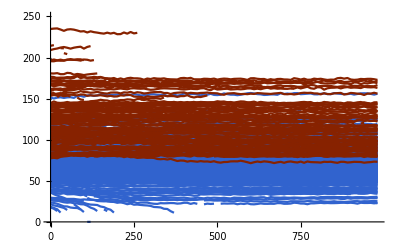

```mathematica
Show[
ListLinePlot[({#[[1]],dx^2*#[[2,2]]}&/@#)&/@Select[domainTracks,#[[1,2,4]]<=5&],PlotStyle->RGBColor[{49,99,206}/255],PlotRange->{0,250}],
(*ListLinePlot[({#[[1]],dx^2*#[[2,2]]}&/@#)&/@Select[domainTracks,#[[1,2,4]]==6&],PlotStyle->Black,PlotRange->{0,250}],*)
ListLinePlot[({#[[1]],dx^2*#[[2,2]]}&/@#)&/@Select[domainTracks,#[[1,2,4]]>=7&],PlotStyle->Darker@RGBColor[{202,51,0}/255],PlotRange->{0,250}]
]
```

```mathematica
domainTracksCon={{times[[1]],#}}&/@domainVals[[1]];
Monitor[Do[Block[{
doms=domainVals[[i]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[domainTracksCon]],If[#[[-1,1]]==timePrev,Norm[domain[[1]]-#[[-1,2,1]]],Infinity]&/@domainTracksCon};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<20&&distancesSorted[[2,2]]>20 &&Abs[domainTracksCon[[distancesSorted[[1,1]],-1,2,2]]-domain[[2]]]<100,(*ensure that only one junction from the previous time is close to the one we are looking at at the current time;
start new track also if the number of corners changes*)
AppendTo[domainTracksCon[[distancesSorted[[1,1]]]],{time,domain}],
AppendTo[domainTracksCon,{{time,domain}}](*start a new track*)
];
,{domain,doms}]
],{i,2,Length@times}];,i];
```

```mathematica
Show[
ListLinePlot[({#[[1]],dx^2*#[[2,2]]}&/@#)&/@Select[domainTracksCon,#[[1,2,4]]<=5&],PlotStyle->RGBColor[{49,99,206}/255],PlotRange->{0,250}],
(*ListLinePlot[({#[[1]],dx^2*#[[2,2]]}&/@#)&/@Select[domainTracksCon,#[[1,2,4]]==6&],PlotStyle->Black,PlotRange->{0,250}],*)
ListLinePlot[({#[[1]],dx^2*#[[2,2]]}&/@#)&/@Select[domainTracksCon,#[[1,2,4]]>=7&],PlotStyle->Darker@RGBColor[{202,51,0}/255],PlotRange->{0,250}]
]
```

-Graphics-

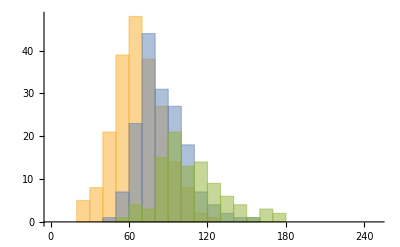

```mathematica
Histogram[{
dx^2Select[domainVals[[99]],#[[4]]<=5&][[All,2]],
dx^2Select[domainVals[[99]],#[[4]]==6&][[All,2]],
dx^2Select[domainVals[[99]],#[[4]]>=7&][[All,2]]},{0,250,10}]
```

```mathematica
Mean/@{dx^2Select[domainVals[[99]],#[[4]]<=5&][[All,2]],
dx^2Select[domainVals[[99]],#[[4]]==6&][[All,2]],
dx^2Select[domainVals[[99]],#[[4]]>=7&][[All,2]]}
```

{67.6671,85.3758,107.42}

```mathematica
StandardDeviation/@{dx^2Select[domainVals[[99]],#[[4]]<=5&][[All,2]],
dx^2Select[domainVals[[99]],#[[4]]==6&][[All,2]],
dx^2Select[domainVals[[99]],#[[4]]>=7&][[All,2]]}
```

{18.624,18.9263,24.8969}